```mathematica
ClearAll["Global`*"];
Needs["VariationalMethods`"];
pars = {g->9.8, l-> 1, mc-> 1, mp->1 };
T[t_]=1/2 mc x'[t]^2 + 1/2 mp((l θ'[t] Cos[θ[t]]+x'[t])^2 + (l θ'[t] Sin[θ[t]])^2);
V[t_]= -mp g l Cos[θ[t]];
L[t_]= T[t]-V[t];
eqns={EulerEquations[L[t],x[t],t]/.{0->F[t]},EulerEquations[L[t],θ[t],t]}
cartpole = NonlinearStateSpaceModel[eqns/.pars, {{x[t],0}, {θ[t],π}}, {F[t]},{x[t], θ[t]}, t]
k = LQRegulatorGains[StateSpaceModel[cartpole/.pars], {IdentityMatrix[4],{{1}}}];
csys = SystemsModelStateFeedbackConnect[cartpole, k]
```

{l mp Sin[θ[t]] θ'[t]^2-(mc+mp) x''[t]-l mp Cos[θ[t]] θ''[t]==F[t],-l mp (g Sin[θ[t]]+Cos[θ[t]] x''[t]+l θ''[t])==0}

0.+x_2[t]-(19.6 Sin[x_1[t]])/(2-Cos[x_1[t]]^2)+(Cos[x_1[t]] (F[t]-Sin[x_1[t]] x_2[t]^2))/(2-Cos[x_1[t]]^2)0.+x_4[t](9.8 Cos[x_1[t]] Sin[x_1[t]])/(2-Cos[x_1[t]]^2)-(F[t]-Sin[x_1[t]] x_2[t]^2)/(2-Cos[x_1[t]]^2)x_3[t]x_1[t]{x_1[t],π}x_2[t]{x_3[t],0}x_4[t] 4122NoneNoneFalseFalseFalse{F[t]}t

0.+x_2[t]-(19.6 Sin[x_1[t]])/(2-Cos[x_1[t]]^2)+(Cos[x_1[t]] (u_1[t]+51.0162 (-π+x_1[t])+12.8235 x_2[t]-Sin[x_1[t]] x_2[t]^2-1. x_3[t]-2.7224 x_4[t]))/(2-Cos[x_1[t]]^2)0.+x_4[t](9.8 Cos[x_1[t]] Sin[x_1[t]])/(2-Cos[x_1[t]]^2)-(u_1[t]+51.0162 (-π+x_1[t])+12.8235 x_2[t]-Sin[x_1[t]] x_2[t]^2-1. x_3[t]-2.7224 x_4[t])/(2-Cos[x_1[t]]^2)x_3[t]x_1[t]{x_1[t],π}x_2[t]{x_3[t],0}x_4[t] 4122NoneNoneFalseFalseFalse{u_1[t]}t

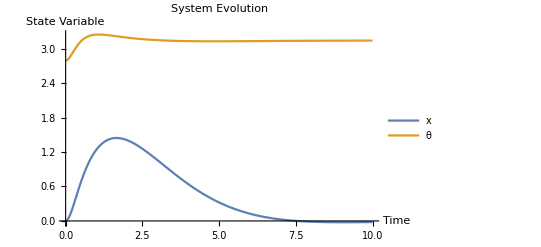

```mathematica
resp = OutputResponse[{csys, {160°,0,0,0}},0,{t,0,10}];
xs[t_]= resp[[1]];
θs[t_]=resp[[2]];
p[t_] = {xs[t]+l Sin[θs[t]],-l Cos[θs[t]]}/.pars;

Plot[resp, {t,0,10}, PlotLegends->{"x", "θ"}, PlotLabel-> "System Evolution", AxesLabel->{"Time", "State Variable"}]
```

```mathematica
Animate[Graphics[{Thick,Green,Line[{{xs[t],0},p[t]}], Thick, Green, Rectangle[{xs[t]-0.3, -0.1},{xs[t]+0.3, 0.1}]}, PlotRange->{{-1.5,1.5},{-1.5,1.5}}, GridLines->Automatic], {t, 0, 10}, AnimationRunning->False]
(*Export["cartpole.gif",Table[Graphics[{Thick,Green,Line[{{xs[t],0},p[t]}], Thick, Green, Rectangle[{xs[t]-0.3, -0.1},{xs[t]+0.3, 0.1}]}, PlotRange->{{-1.5,1.5},{-1.5,1.5}}, GridLines->Automatic], {t, 0, 10,0.041667}], "FrameRate"->24] *)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["cartpole.gif"]]]
```